```mathematica
NSum[r/(2 π)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])HeavisideTheta[2/Max[x,0.005]-0.164414](0.01)(0.01),{x,0,12.2,0.01},{r,0,20,0.01}]
```

$Aborted

```mathematica
2/0.164414
```

12.1644

```mathematica
Sum[r/(2 π)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])HeavisideTheta[2/Max[x,0.005]-0.164414](0.001)(0.01),{x,0,12.2,0.001},{r,0,20,0.01}]
```

```mathematica
Subscript[n, 3(10)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r t)))] (-0.164414+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)
Subscript[ñ, 3(10)][r_]=(4Pi r^2)Subscript[n, 3(10)][r]
Subscript[n, 3(2)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.48075)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r t)))] (-0.48075+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)
Subscript[ñ, 3(2)][r_]=(4Pi r^2)Subscript[n, 3(2)][r]
Subscript[n, 3(28)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.0827625)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r t)))] (-0.0827625+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)
Subscript[ñ, 3(28)][r_]=(4Pi r^2)Subscript[n, 3(28)][r]
```

∫_({a,t}∈ImplicitRegion[147.973>r^2+a^2-2 r a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.164414+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r t)))])/(2 a π^2)

4 π r^2 ∫_({a,t}∈ImplicitRegion[147.973>r^2+a^2-2 r a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.164414+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r t)))])/(2 a π^2)

∫_({a,t}∈ImplicitRegion[17.307>r^2+a^2-2 r a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.48075+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r t)))])/(2 a π^2)

4 π r^2 ∫_({a,t}∈ImplicitRegion[17.307>r^2+a^2-2 r a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.48075+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r t)))])/(2 a π^2)

∫_({a,t}∈ImplicitRegion[583.973>r^2+a^2-2 r a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.0827625+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r t)))])/(2 a π^2)

4 π r^2 ∫_({a,t}∈ImplicitRegion[583.973>r^2+a^2-2 r a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.0827625+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r t)))])/(2 a π^2)

```mathematica
NIntegrate[Subscript[ñ, 3(10)][r],{r,0,20}]
```

9.97604

```mathematica
NIntegrate[Subscript[ñ, 3(2)][r],{r,0,12}]
```

1.99957

```mathematica
NIntegrate[Subscript[ñ, 3(28)][r],{r,0,40}]
```

27.987

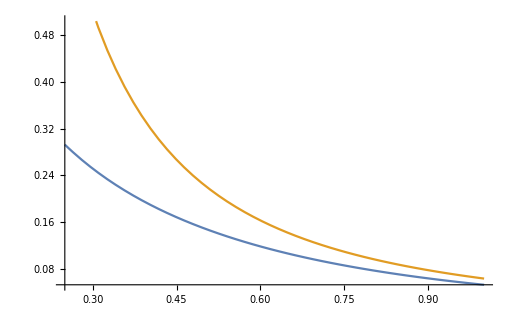

```mathematica
Plot[{Subscript[n, 3(2)][r],((Sqrt[-0.48075+2/r])^3)*HeavisideTheta[-0.48075+2/r]/(3Pi^2)},{r,0.25,1}]
```

```mathematica
4Pi Subscript[n, 3(2)][0]
```

5.37077×10^8

```mathematica
Subscript[n, TF(2)][r_]=4Pi((Sqrt[-0.48075+2/r])^3)*HeavisideTheta[-0.48075+2/r]/(3Pi^2)
```

(4 (-0.48075+2/r)^(3/2) HeavisideTheta[-0.48075+2/r])/(3 π)

```mathematica
4Pi Subscript[n, 3(10)][0]
```

5.37077×10^8

```mathematica
∫_({a,t}∈ImplicitRegion[17.30698453107131>r^2+a^2-2  a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.48075+2/(√(a^2-2 a  t)))^(3/2) BesselJ[3,2 a √(-0.48075+2/(√(a^2+-2 a  t)))])/(2 a π^2)
```

∫_({a,t}∈ImplicitRegion[17.307>r^2+a^2-2 a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.48075+2/(√(a^2-2 a t)))^(3/2) BesselJ[3,2 a √(-0.48075+2/(√(a^2-2 a t)))])/(2 a π^2)

```mathematica
Simplify[∫_({a,t}∈ImplicitRegion[17.30698453107131>r^2+a^2-2 a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.48075+2/(√(a^2-2 a t)))^(3/2) BesselJ[3,2 a √(-0.48075+2/(√(a^2-2 a t)))])/(2 a π^2)]
```

∫_({a,t}∈ImplicitRegion[17.307>r^2+a^2-2 a t&&a≥0&&-1≤t≤1,{a,t}]) ((-0.48075+2/(√(a (a-2 t))))^(3/2) BesselJ[3,2 a √(-0.48075+2/(√(a (a-2 t))))])/(2 a π^2)

```mathematica
Subscript[n, TF(2)][0]
```

ComplexInfinity

```mathematica
4Pi Subscript[n, 3(28)][0]
```

5.37077×10^8

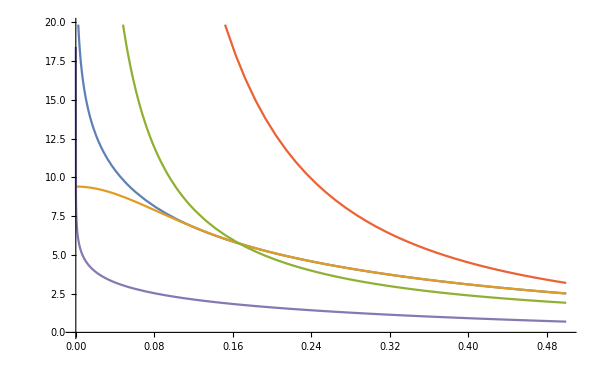

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r],Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}],6/(2Pi r),4*((Sqrt[-0.164414+2/r])^3)*HeavisideTheta[-0.164414+2/r]/(3Pi),-Log[E,r]},{r,0,0.5}]
```

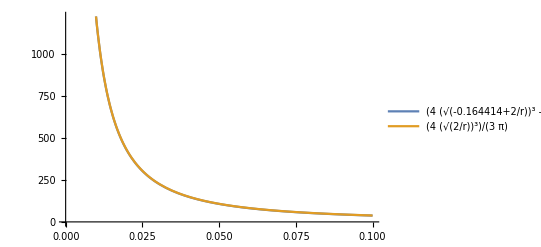

```mathematica
Plot[{4*((Sqrt[-0.164414+2/r])^3)*HeavisideTheta[-0.164414+2/r]/(3Pi),(4/(3Pi))*Sqrt[2/r]^3},{r,0,0.1},PlotLegends->"Expressions"]
```

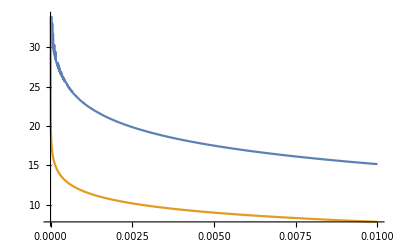

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r],-(16/(3Pi))Log[E,r]},{r,0,0.01}]
```

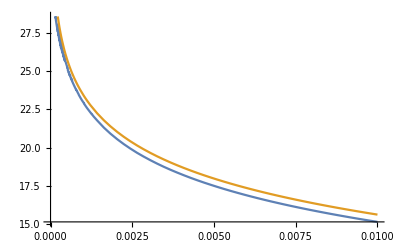

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r],-(32/(3Pi))Log[E,r]},{r,0,0.01}]
```

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r]/((16/(3Pi))Log[E,r]/r},{r,20,21}]
```

$Aborted

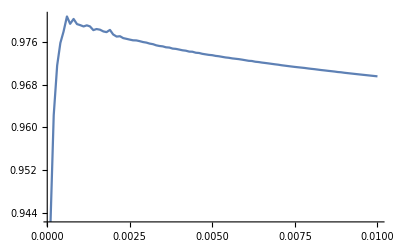

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r]/(-(32/(3Pi))Log[E,r])},{r,0.0001,0.01},PlotRange->All,MaxRecursion->0,PlotPoints->100]
```

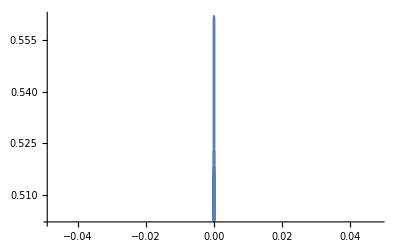

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r]/(-(32/(3Pi))Log[E,r])},{r,10^-300,10^-298},PlotRange->All,MaxRecursion->0,PlotPoints->100]
```

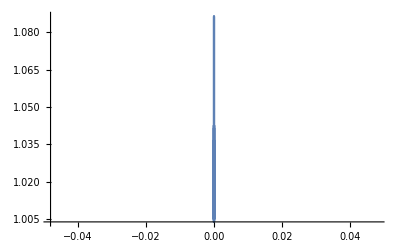

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r]/(-(16/(3Pi))Log[E,r])},{r,10^-299,10^-298},PlotRange->All,MaxRecursion->0,PlotPoints->100]
```

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r]/(-(32/(3Pi))Log[E,r])},{r,0.0001,0.01},PlotRange->All,MaxRecursion->0,PlotPoints->100]
```

```mathematica
(32/(3Pi))Log[E,1/r]
```

(32 log(1/r))/(3 π)

```mathematica
Integrate[((-0.164414+2/(√(2 r^2(1- t))))^(3/2) BesselJ[3,2 a √(-0.164414+2/(√(2 r^2(1- t))))])/(2 r π^2),{t,1,1-0.164414/r}]
```

∫_1^(1-0.164414/r) ((-0.164414+(√2)/(√(r^2 (1-t))))^(3/2) BesselJ[3,2 a √(-0.164414+(√2)/(√(r^2 (1-t))))])/(2 π^2 r)ⅆt

```mathematica
D[2/(√(2 r^2(1- t))),t]
```

r^2/(√2 (r^2 (1-t))^(3/2))

```mathematica
Plot[Integrate[((-0.164414+2/(√(2 r^2(1- t))))^(3/2) BesselJ[3,2 a √(-0.164414+2/(√(2 r^2(1- t))))])/(2 r π^2),{t,1,1-0.164414/r}],{r,100,101}]
```

NIntegrate::inumr: The integrand 0.000506606 (-0.164414+0.0141421/(√(1-t)))^(3/2) BesselJ[3,2 a √(-0.164414+0.0141421/(√Plus[«2»]))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,0.998356}}.

NIntegrate::inumr: The integrand 0.000506606 (-0.164414+0.0141421/(√(1.-1. t)))^(3/2) BesselJ[3.,2. a √(-0.164414+0.0141421/(√Plus[«2»]))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.998356}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

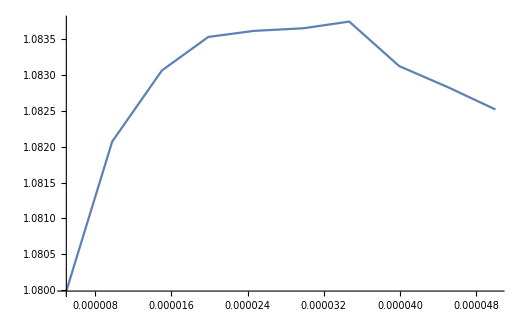

```mathematica
Plot[{4Pi Subscript[n, 3(10)][r]/(-(16/(3Pi))Log[E,r]+11.7269695821)},{r,0.000005,0.00005},PlotRange->All,MaxRecursion->0,PlotPoints->10]
```

```mathematica
((2/(√(2 r^2(1- t))))^(3/2) BesselJ[3,2 a √(2/(√(2 r^2(1- t))))])/(2 r π^2)
```

```mathematica
(x/r)(2/x)BesselJ[2,2(r-x)√(2/x)]/(x-r)^2
```

(2 BesselJ[2,2 √2 (r-x) √(1/x)])/(r (-r+x)^2)

```mathematica
Simplify[(2 BesselJ[2,2 √2 (r-x) √(1/x)])/(r (-r+x)^2)]
```

(2 BesselJ[2,2 √2 (r-x) √(1/x)])/(r (r-x)^2)

```mathematica
(2 √2 (r-x) √(1/x))^2
```

```mathematica
Solve[(8 (r-x)^2)/x==Z,x]
```

{{x→1/16 (16 r+Z-√Z √(32 r+Z))},{x→1/16 (16 r+Z+√Z √(32 r+Z))}}

```mathematica
D[1/16 (16 r+Z-√Z √(32 r+Z)),Z]
```

1/16 (1-(√Z)/(2 √(32 r+Z))-(√(32 r+Z))/(2 √Z))

```mathematica
D[1/16 (16 r+Z+√Z √(32 r+Z)),Z]
```

1/16 (1+(√Z)/(2 √(32 r+Z))+(√(32 r+Z))/(2 √Z))

```mathematica
Integrate[(2 BesselJ[2,√Z])/(r (-r+1/16 (16 r+Z-√Z √(32 r+Z)))^2)1/16 (1-(√Z)/(2 √(32 r+Z))-(√(32 r+Z))/(2 √Z)),Z]+Integrate[(2 BesselJ[2,√Z])/(r (-r+1/16 (16 r+Z+√Z √(32 r+Z)))^2)
```